```mathematica
f[x_]:=(1-x)/(1+x)- ϵ x^3
```

```mathematica
eq=(1-x)/(1+x)- ϵ x^3
```

(1-x)/(1+x)-x^3 ϵ

```mathematica
p=eq/.x->{x0+ϵ x1+ϵ^2 x2+ϵ^3 x3+ϵ^4 x4+O[ϵ]^5}
```

{(1-x0)/(1+x0)+(-x0^3-((1-x0) x1)/(1+x0)^2-x1/(1+x0)) ϵ+(-3 x0^2 x1+x1^2/(1+x0)^2-x2/(1+x0)+((1-x0) (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)) ϵ^2+((x1 x2)/(1+x0)^2-x0^3 ((3 x1^2)/x0^2+(3 x2)/x0)-(x1 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)-x3/(1+x0)+((1-x0) (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0)) ϵ^3+(-(x2 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)+(x1 x3)/(1+x0)^2-x0^3 ((4 x1 x2)/x0^2+(x1 (x1^2/x0^2+(2 x2)/x0))/x0+(3 x3)/x0)-(x1 (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0)-x4/(1+x0)+((1-x0) (x1^4/(1+x0)^4-(3 x1^2 x2)/(1+x0)^3+x2^2/(1+x0)^2+(2 x1 x3)/(1+x0)^2-x4/(1+x0)))/(1+x0)) ϵ^4+O[ϵ]^5}

```mathematica
plist=CoefficientList[p,ϵ]
```

{{(1-x0)/(1+x0),-x0^3-((1-x0) x1)/(1+x0)^2-x1/(1+x0),-3 x0^2 x1+x1^2/(1+x0)^2-x2/(1+x0)+((1-x0) (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0),(x1 x2)/(1+x0)^2-x0^3 ((3 x1^2)/x0^2+(3 x2)/x0)-(x1 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)-x3/(1+x0)+((1-x0) (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0),-(x2 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)+(x1 x3)/(1+x0)^2-x0^3 ((4 x1 x2)/x0^2+(x1 (x1^2/x0^2+(2 x2)/x0))/x0+(3 x3)/x0)-(x1 (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0)-x4/(1+x0)+((1-x0) (x1^4/(1+x0)^4-(3 x1^2 x2)/(1+x0)^3+x2^2/(1+x0)^2+(2 x1 x3)/(1+x0)^2-x4/(1+x0)))/(1+x0)}}

```mathematica
Solve[(1-x0)/(1+x0)==0,x0]
```

{{x0→1}}

```mathematica
Solve[{-x0^3-((1-x0) x1)/(1+x0)^2-x1/(1+x0)==0/.x0->1},x1]
```

{{x1→-2}}

```mathematica
Solve[{-3 x0^2 x1+x1^2/(1+x0)^2-x2/(1+x0)+((1-x0) (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)==0/.x0->1/.x1->-2},x2]
```

{{x2→14}}

```mathematica
Solve[{(x1 x2)/(1+x0)^2-x0^3 ((3 x1^2)/x0^2+(3 x2)/x0)-(x1 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)-x3/(1+x0)+((1-x0) (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0)==0/.x0->1/.x1->-2/.x2->14},x3]
```

{{x3→-134}}

```mathematica
Solve[{(x2 (x1^2/(1+x0)^2-x2/(1+x0)))/(1+x0)+(x1 x3)/(1+x0)^2-x0^3 ((4 x1 x2)/x0^2+(x1 (x1^2/x0^2+(2 x2)/x0))/x0+(3 x3)/x0)-(x1 (-x1^3/(1+x0)^3+(2 x1 x2)/(1+x0)^2-x3/(1+x0)))/(1+x0)-x4/(1+x0)+((1-x0) (x1^4/(1+x0)^4-(3 x1^2 x2)/(1+x0)^3+x2^2/(1+x0)^2+(2 x1 x3)/(1+x0)^2-x4/(1+x0)))/(1+x0)==0/.x0->1/.x1->-2/.x2->14/.x3->-134},x4]
```

{{x4→1314}}

```mathematica
g1[ϵ_]:={f[x]/.x->1-2ϵ+14 ϵ^2-134 ϵ^3+1314 ϵ^4}
```

```mathematica
graphg1=Plot[g1[ϵ],{ϵ,0,0.1},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Red];
g2[ϵ_]:={f[x]/.x->1/ϵ^(1/3)  (-1-ϵ^(1/3)  2/5)}
graphg2=Plot[g2[ϵ],{ϵ,0,0.1},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Green];
h1[ϵ_]:={f[x]/.x->1- 2/3 ϵ}
graphh1=Plot[h1[ϵ],{ϵ,0,0.1},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Orange];
```

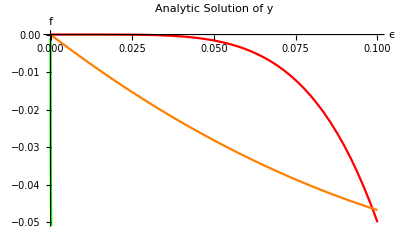

```mathematica
Show[graphg1,graphg2,graphh1]
```

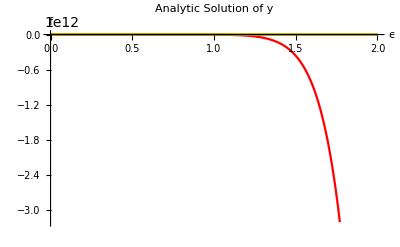

```mathematica
graphg1=Plot[g1[ϵ],{ϵ,0,2},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Red];
graphg2=Plot[g2[ϵ],{ϵ,0,2},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Green];
graphh1=Plot[h1[ϵ],{ϵ,0,2},AxesLabel->{"ϵ","f"},PlotLabel->"Analytic Solution of y",PlotStyle->Orange];
Show[graphg1,graphg2,graphh1]
```

```mathematica
eq2=(1-x)/(1+x)- ϵ x^3/.x->y ϵ^γ/.γ->-1/3//Simplify
```

-y^3+(-y+ϵ^(1/3))/(y+ϵ^(1/3))

```mathematica
-y^3+(-y+ϵ^(1/3))/(y+ϵ^(1/3))
```

-y^3+(-y+ϵ^(1/3))/(y+ϵ^(1/3))

```mathematica
q=eq2/.y->{y0+ϵ^(1/3)  y1}
```

{-(y0+y1 ϵ^(1/3))^3+(-y0+ϵ^(1/3)-y1 ϵ^(1/3))/(y0+ϵ^(1/3)+y1 ϵ^(1/3))}

```mathematica
w=Series[{-(y0+y1 ϵ^(1/3))^3+(-y0+ϵ^(1/3)-y1 ϵ^(1/3))/(y0+ϵ^(1/3)+y1 ϵ^(1/3))},{ϵ,0,3}]
```

{(-1-y0^3)+(2/y0-3 y0^2 y1) ϵ^(1/3)+(-3 y0 y1^2-(2 (1+y1))/y0^2) ϵ^(2/3)+(1/y0^3+(3 y1)/y0^3+(3 y1^2)/y0^3-y1^3+y1^3/y0^3+((1-y1) (1+2 y1+y1^2))/y0^3) ϵ+(-1/y0^4-(4 y1)/y0^4-(6 y1^2)/y0^4-(4 y1^3)/y0^4-y1^4/y0^4+((1-y1) (-1/y0^3-(3 y1)/y0^3-(3 y1^2)/y0^3-y1^3/y0^3))/y0) ϵ^(4/3)+(1/y0^5+(5 y1)/y0^5+(10 y1^2)/y0^5+(10 y1^3)/y0^5+(5 y1^4)/y0^5+y1^5/y0^5+((1-y1) (1/y0^4+(4 y1)/y0^4+(6 y1^2)/y0^4+(4 y1^3)/y0^4+y1^4/y0^4))/y0) ϵ^(5/3)+(-1/y0^6-(6 y1)/y0^6-(15 y1^2)/y0^6-(20 y1^3)/y0^6-(15 y1^4)/y0^6-(6 y1^5)/y0^6-y1^6/y0^6+((1-y1) (-1/y0^5-(5 y1)/y0^5-(10 y1^2)/y0^5-(10 y1^3)/y0^5-(5 y1^4)/y0^5-y1^5/y0^5))/y0) ϵ^2+(1/y0^7+(7 y1)/y0^7+(21 y1^2)/y0^7+(35 y1^3)/y0^7+(35 y1^4)/y0^7+(21 y1^5)/y0^7+(7 y1^6)/y0^7+y1^7/y0^7+((1-y1) (1/y0^6+(6 y1)/y0^6+(15 y1^2)/y0^6+(20 y1^3)/y0^6+(15 y1^4)/y0^6+(6 y1^5)/y0^6+y1^6/y0^6))/y0) ϵ^(7/3)+(-1/y0^8-(8 y1)/y0^8-(28 y1^2)/y0^8-(56 y1^3)/y0^8-(70 y1^4)/y0^8-(56 y1^5)/y0^8-(28 y1^6)/y0^8-(8 y1^7)/y0^8-y1^8/y0^8+((1-y1) (-1/y0^7-(7 y1)/y0^7-(21 y1^2)/y0^7-(35 y1^3)/y0^7-(35 y1^4)/y0^7-(21 y1^5)/y0^7-(7 y1^6)/y0^7-y1^7/y0^7))/y0) ϵ^(8/3)+(1/y0^9+(9 y1)/y0^9+(36 y1^2)/y0^9+(84 y1^3)/y0^9+(126 y1^4)/y0^9+(126 y1^5)/y0^9+(84 y1^6)/y0^9+(36 y1^7)/y0^9+(9 y1^8)/y0^9+y1^9/y0^9+((1-y1) (1/y0^8+(8 y1)/y0^8+(28 y1^2)/y0^8+(56 y1^3)/y0^8+(70 y1^4)/y0^8+(56 y1^5)/y0^8+(28 y1^6)/y0^8+(8 y1^7)/y0^8+y1^8/y0^8))/y0) ϵ^3+O[ϵ]^(10/3)}

```mathematica
qlist=CoefficientList[q,ϵ]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

CoefficientList::poly: -(y0+y1 ϵ^(1/3))^3+(-y0+ϵ^(1/3)-y1 ϵ^(1/3))/(y0+ϵ^(1/3)+y1 ϵ^(1/3)) is not a polynomial.

{{-y0^3-y0/(y0+ϵ^(1/3)+y1 ϵ^(1/3))-3 y0^2 y1 ϵ^(1/3)+ϵ^(1/3)/(y0+ϵ^(1/3)+y1 ϵ^(1/3))-(y1 ϵ^(1/3))/(y0+ϵ^(1/3)+y1 ϵ^(1/3))-3 y0 y1^2 ϵ^(2/3),-y1^3}}

```mathematica
Solve[(1-x0)/(1+x0)==0,y0]
```

{}